```mathematica
Quit[];
```

```mathematica
rutaFA=ExpandFileName["~/Documentos/FeynArts-3.12"];
rutaModels=ExpandFileName["~/Documentos/FeynArts-3.12/Models"];

If[!MemberQ[$Path,rutaFA],PrependTo[$Path,rutaFA]];
<<FeynArts`

SetDirectory[rutaModels];
```

FeynArts 3.12 (27 Mar 2025)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

loading generic model file /home/josias/Documentos/FeynArts-3.12/Models/Grafica_Gauge.gen

> $GenericMixing is OFF

generic model {Grafica_Gauge} initialized

loading classes model file /home/josias/Documentos/FeynArts-3.12/Models/Grafica_Gauge.mod

> 43 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 8 vertices

classes model {Grafica_Gauge} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

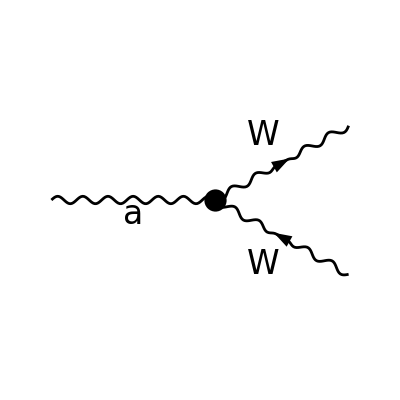

-ⅈ gc3 (g_νρ (k_2-k_3)(μ)+g_μν (k_1-k_2)(ρ)+g_ρμ (k_3-k_1)(ν))

```mathematica
(*2. Crear topología 1->2 a nivel árbol*)topAWW=CreateTopologies[0,1->2];

(*V[1]=Fotón (A),V[3] y-V[3]=Bosones W+y W-*)
diagramasAWW=InsertFields[topAWW,{V[1]}->{V[3],-V[3]},Model->"Grafica_Gauge",GenericModel->"Grafica_Gauge"];

(*3. Dibujar el diagrama limpio*)
Paint[diagramasAWW,PaintLevel->{Classes},ColumnsXRows->{1,1},SheetHeader->False,Numbering->None];

(*4. Extraer el acoplamiento de M$CouplingMatrices y armar la estructura de Lorentz VVV*)
acoplamientoAWW=First[Cases[M$CouplingMatrices,(C[OrderlessPatternSequence[V[1],V[3],-V[3]]]==val_):>val[[1,1]]]];

(*Estructura cinemática de Lorentz para 3 bosones vectoriales (momentos entrantes k1,k2,k3)*)
tensorLorentzVVV=(Subscript[g,μν] (Subscript[k,1]-Subscript[k,2])[ρ]+Subscript[g,νρ] (Subscript[k,2]-Subscript[k,3])[μ]+Subscript[g,ρμ] (Subscript[k,3]-Subscript[k,1])[ν]);

verticeAWW=Simplify[acoplamientoAWW*tensorLorentzVVV/. {EL->e,gw->Subscript[g,W],sw->Subscript[s,w]}];

Style[TraditionalForm[verticeAWW],18,FontFamily->"CMU Serif"]
```